data is from here
https://www.ecdc.europa.eu/en/geographical-distribution-2019-ncov-cases

https://www.ecdc.europa.eu/en/publications-data/download-todays-data-geographic-distribution-covid-19-cases-worldwide

## initialize the notebook

```mathematica
dateFile="2020-10-30"
```

2020-10-30

```mathematica
plotEndYear=2021.1
```

2021.1

```mathematica
data={1900+FromDate[{IntegerPart[#[[4]]],IntegerPart[#[[3]]],IntegerPart[#[[2]]],0,0,0}]/(365.24*3600*24),#[[5]] (* deaths = 6, cases = 5 *),#[[7]],#[[8]]}&/@Drop[Import["C:\\Users\\thatj\\Desktop\\ECONDATA\\COVID-19-geographic-disbtribution-worldwide-"<>dateFile<>".xlsx"][[1]],1];
```

```mathematica
totals={#[[1,1]],Total[#[[All,2]]]}&/@Split[Sort[data[[All,{1,2}]]],#1[[1]]==#2[[1]]&];
```

```mathematica
accumulated=Transpose[{totals[[All,1]],Accumulate[totals[[All,2]]]}];
```

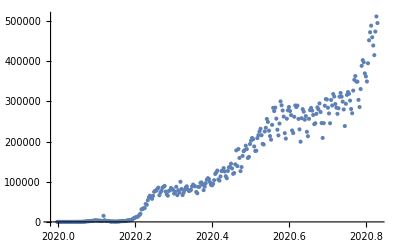

```mathematica
ListPlot[totals,PlotRange->All]
```

```mathematica
(* list of top countries *)
```

```mathematica
monthList={"J","F","M","A","M","J","J","A","S","O","N","D"};
monthList=Join[monthList,monthList];
labels=Table[{1900+FromDate[{2020,ii,1,0,0,0}]/(365.24*3600*24),If[Mod[ii,12]==1,monthList[[ii]]<>"\n"<>ToString[Round[2020+((ii-1)/12)]],monthList[[ii]]]},{ii,1,Length[monthList]}];
```

```mathematica
data[[1]]
```

{2020.83,123.,Afghanistan,AF}

```mathematica
countryData=Sort[Cases[data,x_/;x[[-1]]=="DK"][[All,{1,2}]]];
```

```mathematica
accumulatedData=countryData;
accumulatedData[[All,2]]=Accumulate[countryData[[All,2]]];
```

## DIEM model fit (cases)

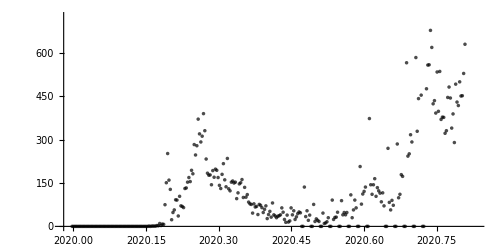

```mathematica
ListPlot[countryData,PlotStyle->Directive[PointSize[0.005],Black,Opacity[0.7]],ImageSize->7*72,AspectRatio->1/2,BaseStyle->FontSize->12]
```

```mathematica
modeFitData={#[[1]],Log[#[[2]]]}&/@Cases[countryData,x_/;x[[2]]>0];
```

```mathematica
nlmInitialShock=NonlinearModelFit[
Cases[modeFitData,x_/;x[[1]]<2020.4],
a0/(1+Exp[(t-t0)/b0])+α(t-2020)+c,
{
{a0,1.0},{b0,-0.02},{t0,2020.25},
{α,-16.0},{c,0}
},t]
```

FittedModel[-10.2199+19.471/(1+ⅇ^(-33.2413 (-«19»+t)))-13.0826 (-2020+t)]

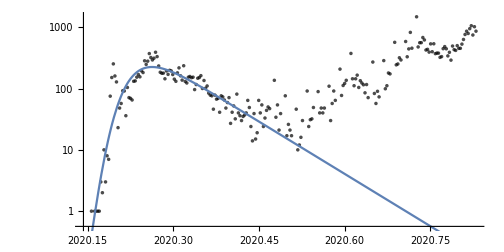

```mathematica
Show[ListLogPlot[countryData,PlotStyle->Directive[PointSize[0.005],Black,Opacity[0.7]]],LogPlot[Exp[Normal[nlmInitialShock]],{t,2020,plotEndYear}],ImageSize->7*72,AspectRatio->1/2,BaseStyle->FontSize->12]
```

```mathematica
nlmSurges=NonlinearModelFit[
modeFitData,
Normal[nlmInitialShock]+a1/(1+Exp[(t-t1)/b1])+a2/(1+Exp[(t-t2)/b2])+a3/(1+Exp[(t-t3)/b3]),
{
{a1,2.0},{b1,-0.02},{t1,2020.55},
{a2,2.0},{b2,-0.02},{t2,2020.7},
{a3,2.0},{b3,-0.02},{t3,2020.8}
},t]
```

FittedModel[-10.2199+1.85502/(1+ⅇ^(-102.135 (-«19»+t)))+2.53202/(1+ⅇ^(-«17» («1»)))+4.21141/(1+ⅇ^(«1»))+19.471/(1+ⅇ^(-33.2413 («1»)))-13.0826 (-2020+t)]

```mathematica
σModel=(#[[2]]-Normal[nlmSurges]/.t->#[[1]])&/@modeFitData//StandardDeviation
```

0.474413

```mathematica
bands2σ=Exp[Normal[nlmSurges]+2{σModel,-σModel}];
```

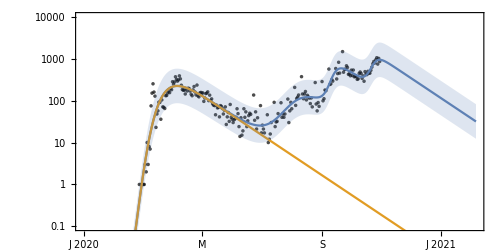

```mathematica
Show[
ListLogPlot[countryData,PlotRange->{{2020,plotEndYear},{0.1,10000}},PlotStyle->Directive[PointSize[0.005],Black,Opacity[0.7]],Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}}],LogPlot[{Exp[Normal[nlmSurges]],Exp[Normal[nlmInitialShock]]},{t,2020,plotEndYear}],
LogPlot[bands2σ,{t,2020,plotEndYear},PlotStyle->None,Filling->{1->{2}}],ImageSize->7*72,AspectRatio->1/2,BaseStyle->FontSize->12]
```

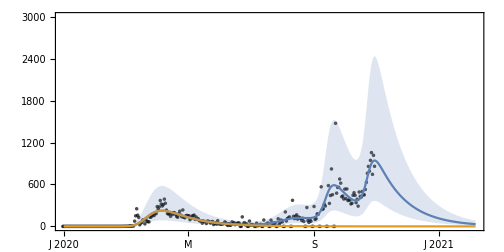

```mathematica
Show[
ListPlot[countryData,PlotRange->{{2020,plotEndYear},{0,3000}},PlotStyle->Directive[PointSize[0.005],Black,Opacity[0.7]],Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}}],
Plot[{Exp[Normal[nlmSurges]],Exp[Normal[nlmInitialShock]]},{t,2020,plotEndYear},PlotRange->All],
Plot[bands2σ,{t,2020,plotEndYear},PlotStyle->None,Filling->{1->{2}},PlotRange->All],ImageSize->7*72,AspectRatio->1/2,BaseStyle->FontSize->12]
```

```mathematica
nObservations=Length[modeFitData]
```

220

```mathematica
accumulatednlmDIEM=Table[{tt-1/365.24,(365.24)NIntegrate[Exp[Normal[nlmSurges]],{t,2020.0,tt}]},{tt,2020,plotEndYear,0.01}];
accumulatednlmDIEMband1=Table[{tt-1/365.24,(365.24)NIntegrate[Exp[Normal[nlmSurges]+(2σModel)/(√nObservations)],{t,2020.0,tt}]},{tt,2020,plotEndYear,0.01}];
accumulatednlmDIEMband2=Table[{tt-1/365.24,(365.24)NIntegrate[Exp[Normal[nlmSurges]-(2σModel)/(√nObservations)],{t,2020.0,tt}]},{tt,2020,plotEndYear,0.01}];
```

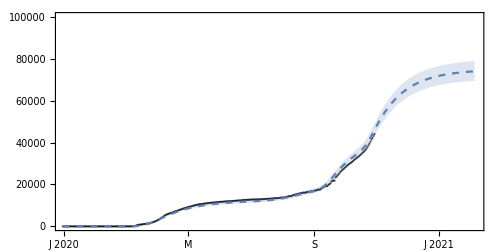

```mathematica
Show[ListPlot[accumulatedData,PlotRange->{{2020,plotEndYear},{0.1,100000}},PlotStyle->Directive[PointSize[0.003],Black,Opacity[0.7]],Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},ImageSize->7*72,AspectRatio->1/2,BaseStyle->FontSize->12],
ListPlot[{#[[1]],#[[2]]}&/@accumulatednlmDIEM,Joined->True,PlotStyle->Dashed],ListPlot[{{#[[1]],#[[2]]}&/@accumulatednlmDIEMband1,{#[[1]],#[[2]]}&/@accumulatednlmDIEMband2},Joined->True,PlotStyle->None,Filling->{1->{2}}]]
```